08

多自由度微振动

许多力学体系具有一个或多个平衡位形。

当处于平衡位形的体系受到微扰时，体系可能在平衡位形附近以一些简正模式做微振动。

本章讨论有限个自由度简单体系的微振动问题。涉及如何求解简正模式，判断振动的稳定性。

这些概念与方法将在后续课程中得到应用。（这些紫色概念术语，将在本章讨论）

本章的讨论均限于力学体系满足以下三个条件，分别是对广义坐标变换、广义力和约束的限制条件。

位形空间的广义坐标变换不显含时间：q_k=q_k(s)

体系中各质点受到的力均为保守力（并且对应的“势能”不显含时间且与速度无关）

体系没受到约束，或者只受到完整约束（几何约束）（G_a(q)=0）。

对这种约束体系，拉格朗日量可消去受限坐标（只保留自由坐标），可从约化的拉格朗日量出发讨论。

本章的主要思路：也是一种“分离变量”，通过线性变换来分离变量

但是，分离变量有时并非像三维谐振子 L=m/2((ẋ)^2+(ẏ)^2+(ż)^2)-1/2(k_1 x^2+k_2 y^2+k_3 z^2)   那么一目了然

代入拉格朗日方程得：m(x^(..))_i+k_1 x_i=0          —— 自动分离变量

拉格朗日量是这样滴，怎么求解  —— 线性变换

L=m/2((ẋ)^2+(ẏ)^2+(ż)^2+2 ẏ ż-2 ẋ ẏ)+1/2[k_1(y^2+z^2+2y z)+k_2 z^2+k_3(x^2-2x y+y^2)]

## § 8.1 平衡和微振动

平衡点邻域的微振动及其稳定问题

### § 8.1.1 平衡

位形空间的平衡点：

位形空间的平衡点（一个平衡位形）由力学体系的一套广义坐标值描述：q_1^(e), q_2^(e),q_3^(e), …, q_D^(e)

这套广义坐标值满足以下条件：

当初始时刻体系各广义坐标取：q_k(0)=q_k^(e)     并且对应的各广义速度为零：(q̇)_k(0)=0  时

体系将永远静止于各广义坐标值：q_k(0)=q_k^(e)，除非体系再受到其它外力扰动。

几种不同的平衡位形：

|   |       |    
稳定平衡            |   | 非稳定平衡              | 随遇平衡

稳定(stable)平衡：微扰将使得体系在平衡位形附件做微振动

非稳定(unstable)平衡：微扰都将使得远离平衡位形

随遇(conditional)平衡：改变广义坐标，重置广义速度为零，体系将在新的坐标处达到平衡

### § 8.1.2 求解平衡点

定义了位形空间的平衡点之后，接着的问题就是如何求出平衡点。

这在第二章拉格朗日力学的 § 2.2.10小节 曾经有过讨论 —— 虚功原理。

鉴于期中考前的内容，期末不再考。这里再次讨论求平衡点的方法。

—— 为期末考涵盖这部分内容找个借口

出发点：拉格朗日力学，还是从大家熟悉的直角坐标系（s-系）出发，但又不能局限于 s-系。

为此要从 s-系出发，经位形空间广义坐标变换（点变换）变到了任意的广义坐标 q-系。

记得本章对变换、力和约束的限制条件，体系的拉格朗日量可写成以下形式

——  参见 § 2.1.3  “任意广义坐标” 一小节

s 系：L(s,ṡ)=1/2(∑_(j=1))^D M_j(ṡ)_j^2-U(s)      因为（第二条件）势不显含时间，故 L 也不显含时间

这里 D 是自由度。默认利用了第三条件，即：

若存在 C 个约束，则先消去受限坐标，只保留自由坐标，D 变成 D-C

变换到 q 系：{ s_α=s_α(q)
(ṡ)_α=(ṡ)_α(q,q̇)                 只讨论变换不显含时间（第一条件）

L(q,q̇)=L[s(q),ṡ(q,q̇)]                    对应于位形空间广义坐标变换（点变换）的 拉格朗日量 L 的变换

广义速度的变换：(ṡ)_j=(ⅆs_j(q))/ⅆt=(∑_(l=1))^D(∂s_j(q))/(∂q_l)(q̇)_l      由第一条件变换不显含时间，故不存在 (∂s)/(∂t)项

动能的变换：      T_2(q,q̇)=1/2(∑_(j=1))^D M_j(ṡ)_j^2=1/2(∑_(j=1))^D M_j(ṡ)_j(ṡ)_j=1/2(∑_(j=1))^D M_j(∑_(l=1))^D(∑_(k=1))^D(∂s_j(q))/(∂q_k)(q̇)_k (∂s_j(q))/(∂q_l)(q̇)_l      
=1/2(∑_(k=1))^D(∑ _(l=1))^D m_(k l)(q)(q̇)_k(q̇)_l      变换不显含时间，动能仅含速度二次项

实对称矩阵：𝕞_(k l)= m_(k l)(q)=(∑_(j=1))^D M_j(∂s_j(q))/(∂q_k)(∂s_j(q))/(∂q_l)      是正定的（证明见下）

矩阵形式：𝕞=((∂s)/(∂q))^T 𝕄 ((∂s)/(∂q))，    𝕄_(i j)=M_j δ_(i j) 是对角矩阵,    ((∂s)/(∂q))_(i j)=(∂s_i)/(∂q_j)

𝕞 的性质：  ∀列矩阵 x⃗≠0, 有： (x⃗)^T 𝕞 x⃗=(x⃗)^T ((∂s)/(∂q))^T 𝕄 ((∂s)/(∂q))x⃗=(y⃗)^T 𝕄 y⃗

其中  y_k=(y⃗)_k= [((∂s)/(∂q))x⃗]_k=(∑_(j=1))^D(∂s_k(q))/(∂q_j)x_j 是实的列矢量

因为 𝕄 是对角元为质量 M_j 的对角阵，故：   (y⃗)^T 𝕄 y⃗=∑_j M_j y_j^2>0

⟹   (x⃗)^T𝕞 x⃗=(y⃗)^T 𝕄 y⃗>0

所以，  𝕞 矩阵是实对称正定矩阵。正定矩阵当然是可逆的。

其实从   |((∂s)/(∂q))|≠0 及 𝕞=((∂s)/(∂q))^T 𝕄 ((∂s)/(∂q)) 即得 𝕞 矩阵是可逆的。

代入 s 系的拉格朗日量 L(s,ṡ)，即得任意广义坐标 q 系的拉格朗日量（注意条件：变换不显含时间）

L(q,q̇)=T_2-U=1/2(∑_(i=1))^D(∑ _(j=1))^D(m_(i j)(q))_(⏟_正定矩阵𝕞)(q̇)_i(q̇)_j-U(q) =1/2 q^T 𝕞 q-U(q)

无论什么广义坐标，动能只含广义速度的二次项，且 𝕞 为对称正定矩阵（注意 𝕞 与 q 有关）

上式的推导已经利用了“三个假设”，分别是对坐标变换、力和约束的假设。

比较：L(s,ṡ)=1/2(∑_(j=1))^D M_j(ṡ)_j^2-U(s) =1/2(∑_(i=1))^D(∑_(j=1))^D(M_j δ_(i j))_(⏟_对角矩阵𝕄)(ṡ)_i(ṡ)_j-U(s)            𝕄 为对角矩阵

拉格朗日方程形式不变，并且“全保守”（第二条件）从而有

ⅆ/ⅆt[(∂L(q,q̇))/(∂(q̇)_k)]-(∂L(q,q̇))/(∂q_k)=0

代入拉格朗日量：L=1/2(∑_(i=1))^D(∑ _(j=1))^D m_(i j)(q)(q̇)_i(q̇)_j-U(q)，可化为

ⅆ/ⅆt(∑_(j=1))^Dm_(k j)(q)(q̇)_j-1/2(∑_(i=1))^D(∑ _(j=1))^D(∂m_(i j)(q))/(∂q_k)(q̇)_i(q̇)_j+(∂U(q))/(∂q_k)=0    ⟹

(∑_(j=1))^D(ṁ)_(k j)(q)(q̇)_j+(∑_(j=1))^D m_(k j)(q)(q^(..))_j-1/2(∑_(i=1))^D(∑ _(j=1))^D(∂m_(i j)(q))/(∂q_k)(q̇)_i(q̇)_j+(∂U(q))/(∂q_k)=0

记得我们是要求解平衡点，即满足广义速度为零 (q̇)_k(0)=0 就能静止的广义坐标值 q^(e)。

平衡条件需要满足：(q̇)_k(0)=0 时 (q^(..))_k(0)=0。把这两个方程代入式 (1.EquationNumbered)，即得：

((∂U(q))/(∂q_k)|)_(q=q^(e))=0          k=1,2,…,D

上式与 § 2.2.10 小节 “虚功原理”的结论相同。上式包含 D 个方程，可用于求 D 个平衡坐标  q^(e)。

对存在约束情况，应先消去受限坐标（对几何约束可以这么做），使得势能仅依赖于自由坐标

这时可得到 D-C 个方程，可用于求 D-C 个平衡的自由坐标

因为无论有无约束，求解方法都一样（存在约束时应先消去受限坐标）

因而我们以下的讨论就不再区分是否存在约束。

其实，上述推导只能说明 (1.EquationNumbered) 是平衡的必要条件，是否充分？

数学上更加严格的做法是，将广义速度都为零条件：(q̇)_k(0)=0  代入 (1.EquationNumbered) 式

并利用 𝕞 矩阵是实对称正定可逆矩阵，得：

(q^(..))_j=-(∑ _(k=1))^D 𝕞_(j k)^-1(∂U(q))/(∂q_k)，     因为  𝕞_(j k)^-1 可逆，其各个列矢量线性无关

(- (q^(..))_j=(∑ _(k=1))^D 𝕞_(j k)^-1(∂U(q))/(∂q_k)|)_(q=q^(e))=0     表明线性无关向量之线性组合为 0，

(只能是线性组合系数：(∂U(q))/(∂q_k)|)_(q=q^(e))=0        —— 充要条件

思考：为什么 (q̇)_k(0)=0 时若各  (q^(..))_k(0)也为 0，则 q 就不再改变？

数学上：运动方程是二阶微分方程；物理上：牛顿第一定律

### § 8.1.3 小坐标

假设我们由上一小节的方法找到了位形空间的平衡点。

现在来探讨当各个广义坐标微微偏离平衡点时，会发生什么？

因为是微小地偏离平衡点，因此我们希望以这微小的偏离作为坐标，这样就可以应用 Taylor 展开了。

为此，引入如下小坐标 r_i,   其中 r_i 是个小量（引入小坐标以利用微微偏离平衡点的性质）

r_i=q_i-q_i^(e)   或     q_i=q_i^(e)+r_i    ⟹     (ṙ)_i=(q̇)_i，另外还有    ∂/(∂q_i)=∂/(∂r_i)  因为 q_i^(e) 为常数。

并且，我们认为小坐标的时间导数 (ṙ)_i=(q̇)_i 是 r_i 的同阶小量  ——  这是一个假设

对于振动解，这两个假设也就隐含着所有频率的振动幅度都是有限的。

首先，我们要确定小坐标 r_i 是好坐标（正如我们默认从 s 坐标到 q 坐标都是好坐标一样）。

这一点可以轻易验证：|(∂r_i(q))/(∂q_j)|=1。

这样，我们就把广义坐标从“直角坐标系” s_i 变换到一般广义坐标系 q_i 再变换到小坐标 r_i。

接着，我们将 q-系的拉格朗日量

L(q,q̇)=T_2-U=1/2(∑_(i=1))^D(∑ _(j=1))^D m_(i j)(q)(q̇)_i(q̇)_j-U(q)                注意 m_(i j) 为正定矩阵

写成 r-系的拉格朗日量

L=L(r,ṙ)=L[q(r),q̇(r,ṙ)]=1/2(∑_(i=1))^D(∑ _(j=1))^D(m_(i j)(q^(e)+r))_(⏟_这个圆括号表示函数)(ṙ)_i(ṙ)_j-U(q^(e)+r)

现在，因为 r 是小量，就可以作 Taylor 展开，仅保留到二阶小量

(((L(r,ṙ)=L(r,ṙ)|)_(r, ṙ=0)+(∑_(i=1))^D(∂L(r,ṙ))/(∂r_i)|)_(r, ṙ=0)r_i+(∑_(i=1))^D(∂L(r,ṙ))/(∂(ṙ)_i)|)_(r, ṙ=0) (ṙ)_i
(((+1/2(∑_(i=1))^D(∑_(j=1))^D(∂^2 L(r,ṙ))/(∂r_i∂r_j)|)_(r, ṙ=0)r_i r_j+(∑_(i=1))^D(∑_(j=1))^D(∂^2 L(r,ṙ))/(∂r_i∂(ṙ)_j)|)_(r, ṙ=0)r_i(ṙ)_j+1/2(∑_(i=1))^D(∑_(j=1))^D(∂^2 L(r,ṙ))/(∂(ṙ)_i∂(ṙ)_j)|)_(r, ṙ=0)(ṙ)_i(ṙ)_j+o(h^2)

这里利用了多元函数的 Taylor 展开，例如，对二元函数有

f (x,y)=f(0,0)+((∂f)/(∂x))_(x=0
y=0) x+((∂f)/(∂y))_(x=0
y=0) y+1/(2!)((∂^2 f)/(∂x^2))_(x=0
y=0) x^2+2/(2!)((∂^2 f)/(∂y∂x))_(x=0
y=0)x y+1/(2!)((∂^2 f)/(∂y^2))_(x=0
y=0)y^2+......

其中 o(h^2) 表示高于 h 的二阶无穷小，h=max{r_i, (ṙ)_i}，其中  (ṙ)_i 是 r_i 的同阶小量

注意到：((L(r,ṙ)|)_(r, ṙ=0)=L(q^(e),(q̇)^(e))|)_((q̇)^(e)=0)=-U(q^(e))=L_e  是个常量

并且由平衡条件 (1.EquationNumbered)式：((∂U(q))/(∂q_k)|)_(q=q^(e))=0

三个绿色项为 0 （试证之），在 r-系，拉格朗日量化为

L(r,ṙ)=L_e+1/2(∑_(i=1))^D(∑_(j=1))^D (T_(i j)(ṙ)_i(ṙ)_j-V_(i j)r_i r_j)+o(h^2)

其中 L_e 是常数，并不会影响拉格朗日方程，可暂时舍去。利用 L(r,ṙ) 表达式 (1.EquationNumbered)，常数矩阵 𝕋, 𝕍 为

(((𝕋_(i j)=T_(i j)=(∂^2 L(r,ṙ))/(∂(ṙ)_i∂(ṙ)_j)|)_(r, ṙ=0)=m_(i j)(q^(e)+r)|)_(r=0)=m_(i j)(q^(e))=(∂^2 L(q,q̇))/(∂(q̇)_i∂(q̇)_j)|)_((q̇)^(e)=0)             是个实对称正定矩阵

(((𝕍_(i j)=V_(i j)=-(∂^2 L(r,ṙ))/(∂r_i∂r_j)|)_(r, ṙ=0)=(∂U(q^(e)+r))/(∂r_i∂r_j)|)_(r=0)=(∂U(q))/(∂q_i∂q_j)|)_(q=q^(e))   是个实对称矩阵

拉格朗日方程，如“南窗皓月，依旧照娉婷。”（在广义坐标 r-系中仍具有相同的形式），

ⅆ/ⅆt((∂L(r,ṙ))/(∂(ṙ)_k))-(∂L(r,ṙ))/(∂r_k)=0

拉格朗日量 (1.EquationNumbered) 式和拉格朗日方程 (1.EquationNumbered) 给出近似的运动方程

(∑_(j=1))^D (T_(i j)(r^(..))_j+V_(i j)r_j)+o(h)=0       注意 𝕋 矩阵实对称且正定， 𝕍 矩阵实对称

因为拉格朗日量展开到小坐标的二次项，故运动方程 (1.EquationNumbered) 准确到小坐标的一次项。

故方程 (1.EquationNumbered) 也称为线性化的近似运动方程 —— 在平衡位形附近作小量展开得到的。

思考：如果小坐标的时间导数 (ṙ)_i=(q̇)_i 不是 r_i 的同阶小量。

在这种情况下，出发点还是 q 系拉格朗日量

L(q,q̇)=T_2-U=1/2(∑_(i=1))^D(∑ _(j=1))^D m_(i j)(q)(q̇)_i(q̇)_j-U(q)

第一项是动能项，以  q_i=q_i^(e)+r_i    ⟹     (q̇)_i=(ṙ)_i    代入得

T_2=1/2(∑_(i=1))^D(∑ _(j=1))^D m_(i j)(q)(q̇)_i(q̇)_j=1/2(∑_(i=1))^D(∑ _(j=1))^D m_(i j)(q)(ṙ)_i(ṙ)_j

第二项是势能能，以 r_i 为小量做展开

((U((q)^(e)+r)=U(q^(e))+(∑_(i=1))^D(∂U(q))/(∂q_i)|)_(q^(e))+1/2(∑_(i=1))^D(∑_(j=1))^D(∂^2 U(q))/(∂q_i∂q_j)|)_(q^(e))r_i r_j+o(r^2)

对平衡位形，U(q^(e)+r) 的第二项为 0，代入拉格朗日量，得

(L(q,q̇)=1/2(∑_(i=1))^D(∑ _(j=1))^D m_(i j)(q)(ṙ)_i(ṙ)_j-[U(q^(e))+1/2(∑_(i=1))^D(∑_(j=1))^D(∂^2 U(r))/(∂q_i∂q_j)|)_(q^(e))r_i r_j]
=L_e+1/2(∑_(i=1))^D(∑_(j=1))^D (T_(i j)(ṙ)_i(ṙ)_j-V_(i j)r_i r_j)                   此即 (1.EquationNumbered) 式

其中：{𝕋_(i j)=T_(i j)=m_(i j)(q^(e)) 
(𝕍_(i j)=(∂U(r))/(∂q_i∂q_j)|)_(q^(e))        L_e=-U(q^(e))

是否可以认为不用假设  (ṙ)_i 是 r_i 的同阶无穷小，同样得到 (1.EquationNumbered) 式？

这里其实还是用到了(ṙ)_i 是 r_i 的同阶小量，从而 (ṙ)_i(ṙ)_j 是二阶小量，蓝色项中才能取 m_(i j)(q)=m_(i j)(q^(e))

### § 8.1.4 简正模

微振动理论就是要求解形如 (1.EquationNumbered) 形式的线性化运动方程，得到小坐标  r_i与时间的关系。

注意小坐标其实是偏离平衡广义坐标的“位移”。

通常(1.EquationNumbered)式：(∑_(j=1))^D (T_(i j)(r^(..))_j+V_(i j)r_j)=0  是一个耦合的二阶常系数齐次微分方程组。

人们需要通过再次的广义坐标变换，得到退耦的微分方程，进而求解。

这一步是从 r-系 变换到 ρ-系。

—— 记得“路漫漫其修远兮”：s 系 ⟶ q 系 ⟶ r 系 ⟶ ρ 系

因为 ρ 系中不同坐标的方程退耦，就将 ρ 坐标系称为简正坐标系。ρ_k 称为第 k 个简正坐标。

而单一个 ρ_k 随时间变化所表现出的力学体系的演化，称为体系运动的第 k 个简正模式。

线性近似下体系的一般微振动就是各种不同幅度不同初相位的简正模式的叠加。

要做的从 r-系 到 ρ-系 的这种变换是线性的，由常数矩阵 ℂ 来实现（ℂ 的 i 行 j 列为 C_(i k) ）：

r_i=(∑_(k=1))^D C_(i k)ρ_k    ⟹       (ṙ)_i=(∑_(k=1))^D C_(i k)(ρ̇)_k                   注意 C_(i k) 不再与 ρ 有关，否则就非线性了

当然，为保证 ρ 是好坐标，要求变换矩阵 ℂ 的行列式不为 0。  Quiz: 还记得为什么每一步都要强调好坐标吗？

如此，在 ρ 坐标中的拉格朗日量为

L(r,ṙ)=1/2(∑_(i=1))^D(∑_(j=1))^D (T_(i j)(ṙ)_i(ṙ)_j-V_(i j)r_i r_j)

L(ρ,ρ̇)=1/2(∑_(i=1))^D(∑_(j=1))^D [T_(i j)((∑_(k=1))^D C_(i k)(ρ̇)_k)((∑_(l=1))^D C_(j l)(ρ̇)_l)-V_(i j)((∑_(k=1))^D C_(i k)ρ_k)((∑_(l=1))^D C_(i l)ρ_l)]
=1/2 (∑_(k=1))^D(∑_(l=1))^D[((∑_(i=1))^D(∑_(j=1))^D C_(i k)T_(i j)C_(j l))(ρ̇)_k(ρ̇)_l-((∑_(i=1))^D(∑_(j=1))^D C_(i k)V_(i j)C_(j l))ρ_k ρ_l]

显然，这些求和式应写成矩阵形式。定义以下 D 维列矢量

𝕣=[r_1
r_2
⋮  
r_D]         ϱ=[ρ_1
ρ_2
⋮  
ρ_D]       此外 𝕋, 𝕍, 和  ℂ  皆为 D×D 矩阵。

那么变换写成：𝕣=ℂ ϱ,    𝕣̇=ℂ ϱ̇，转置可得：𝕣^T=ϱ^T ℂ^T,  (𝕣̇)^T=(ϱ̇)^T ℂ^T,

拉格朗日量改写为

L(ρ,ρ̇)=1/2( (ϱ̇)^T  ℂ^T 𝕋 ℂ ϱ̇- ϱ^T  ℂ^T 𝕍 ℂ ϱ )

接下来的问题是：怎么退耦？——    ℂ^T 𝕋 ℂ 和 ℂ^T 𝕍 ℂ 同时对角化！

下一节将讨论一种方法，可找到一个特殊的常数矩阵 ℂ，

在将 𝕋 变换成单位矩阵 𝕌 的同时，将 𝕍 变换成对角矩阵 Θ ：

ℂ^T 𝕋 ℂ=𝕌，     ℂ^T 𝕍 ℂ=Θ

从而方程 (1.EquationNumbered) 就化为

L(ρ,ρ̇)=1/2( (ϱ̇)^T  𝕌 ϱ̇- ϱ^T Θ ϱ )=1/2(∑_(k=1))^D((ρ̇)_k^2-θ_k ρ_k^2)

进而 ρ 系的拉格朗日方程为    —— 记得“南窗皓月，依旧照娉婷”：ⅆ/ⅆt((∂L(ρ,ρ̇))/(∂(ρ̇)_k))-(∂L(ρ,ρ̇))/(∂ρ_k)=0

(ρ^(..))_k+θ_k ρ_k=0,   k=1,2,…, D

完全退耦了（“脱欧”啦）。这些运动方程容易解得

ρ_k=Piecewise[{{A_k cos ω_k t+B_k sin ω_k t, for  θ_k>_ 0   with  ω_k=√θ_k}, {A_k+B_k t, for  θ_k=0}, {A_k cosh γ_k t+B_k sinh γ_k t, for  θ_k<0   with  γ_k=√-θ_k}}]

其中 A_k, B_k 由初始条件确定。

关于如下二阶线性常系数齐次常微分方程的求解
                  (ρ^(..))_k+θ_k ρ_k=0
相信右图中我的好朋友金路教授，已经讲得非常清楚

另一种理解

方程  (ρ^(..))_k+θ_k ρ_k=0 可理解为以频率 √θ_k 振动，θ_k<0 对应于复数频率。

每一个 ρ_k 都对应于一个简正模式。共有 D 个简正模式。

当然，体系的运动状况 r(t) 通常是这 D 个简正模式以不同相位不同幅度的叠加，𝕣=ℂ ϱ

最后当然可以再逐步根据需要变换到 r, q  乃至 s，对应的运动状况。

在进一步讨论这些解的物理意义之前，我们需先讨论如此美妙的退耦是怎么做到的。

### § 8.1.5 广义本征值问题

常数矩阵 ℂ 很妙，它可以在将 𝕋 矩阵变换成单位矩阵的同时，将 𝕍 矩阵变换成对角矩阵。

或等价地说，就是将 𝕋 矩阵和 𝕍 矩阵同时对角化

做到其中一点也许不难，就是矩阵对角化。
困难似乎在同时做到同时对角化。
即，在将  𝕍 矩阵变换成对角矩阵的同时，
                 将  𝕋  矩阵变换成单位矩阵
此所谓“世间安得两全法，不负如来不负卿”      -Graphics-

世间也许做不到，但数学上做得到，这就是广义本征值法。

𝔸 𝕫^(k)=θ_k 𝕘 𝕫^(k)          称为  广义本征值问题

其中 𝕫^(k)为列矢量，称为矩阵 𝔸 对应于本征值 θ_k 的本征矢量。

与普通本征值问题不同的是，这里出现了一个正定矩阵 𝕘。

当 𝕘=U 单位矩阵时，退化为普通的本征值问题。

我们感兴趣的情况是： 𝔸 是实对称矩阵，𝕘 是实对称正定矩阵。

就是，求解实对称矩阵𝔸 的广义本征值及本征矢量。

广义本征值问题 (1.EquationNumbered) 可化为

(𝔸 -θ_k 𝕘) 𝕫^(k)=0    故本征值由行列式      |𝔸 -θ_k 𝕘|=0    给出。

——  回顾线性代数中线性无关，线性齐次方程非零解相关内容。

对广义本征值问题，有以下两个数学定理。

定理一：如果矩阵 𝔸 是 N×N 实对称矩阵，𝕘 是实对称正定矩阵，则广义本征值方程

𝔸 𝕫^(k)=θ_k 𝕘 𝕫^(k)

存在 N 个实本征值 θ_1,θ_2,…, θ_N 和对应的 N 个归一化的实本征矢量 𝕫^(1),𝕫^(2),…,𝕫^(N)，

这 N 个是本征矢量满足如下正交特性：(𝕫^(k))^T 𝕘 𝕫^(l)=δ_(k l)，记为    (𝕫^(k))^T⊙ 𝕫^(l)=δ_(k l)

定理二：由广义本征矢量 𝕫^(k) 作为列矢量构成的矩阵 ℂ：    ℂ_(i k)= 𝕫_i^(k)，即

ℂ=[z_1^(1) | z_1^(2) | … | z_1^(N)
z_2^(1) | z_2^(2) | … | z_2^(N)
⋮    | ⋮    | ⋮   | ⋮   
z_N^(1) | z_N^(2) | … | z_N^(N)]    满足：ℂ^T 𝕘 ℂ=𝕌,    ℂ^T 𝔸ℂ=Θ=[θ_1 | 0  | … | 0 
0  | θ_2 | … | 0 
⋮  | ⋮  | ⋮  | ⋮ 
0  | 0  | … | θ_N]

其中 𝕌 为单位矩阵

接着，应用广义本征值问题的两个数学定理，确定如下拉格朗日量中的矩阵 ℂ

L(ρ,ρ̇)=1/2( (ϱ̇)^T  ℂ^T 𝕋 ℂ ϱ̇- ϱ^T  ℂ^T 𝕍 ℂ ϱ )   —— 记得我们一直强调： 𝕋 实对称正定， 𝕍 实对称

步骤如下：

𝕍  𝕫^(k)=θ_k 𝕋 𝕫^(k)   ⟹   |𝕍 -θ_k 𝕋|=0   求出实广义本征值 θ_k,  k=1,2,…,D

(𝕍 -θ_k 𝕋) 𝕫^(k)=0               求出广义本征矢量  𝕫^(k)，

记得要将本征矢量归一化使得

(𝕫^(k))^T 𝕋 𝕫^(k)=(∑^D)_(i=1)(∑_(j=1))^D z_i^(k)T_(i j)z_j^(k)=1,   即：       (𝕫^(k))^T⊙ 𝕫^(l)≡(𝕫^(k))^T 𝕋 𝕫^(l)=δ_(k l)

进而构造 ℂ 矩阵：ℂ_(i k)= 𝕫_i^(k)       由 𝕫^(k)列矢量构成

此 ℂ 矩阵代入拉格朗日量   L(ρ,ρ̇)=1/2( (ϱ̇)^T  ℂ^T 𝕋 ℂ ϱ̇- ϱ^T  ℂ^T 𝕍 ℂ ϱ )  并利用

ℂ^T 𝕋 ℂ=𝕌,    ℂ^T 𝕍 ℂ=Θ       即得：

L(ρ,ρ̇)=1/2( (ϱ̇)^T  𝕌 ϱ̇- ϱ^T Θ ϱ )=1/2(∑_(k=1))^D((ρ̇)_k^2-θ_k ρ_k^2)

### § 8.1.6 稳定性

应用广义本征值问题的数学定理，我们可将在平衡位形附近线性化的拉格朗日量化为

L(ρ,ρ̇)=1/2(∑_(k=1))^D((ρ̇)_k^2-θ_k ρ_k^2)

进而得到退耦的拉格朗日方程（完全“脱欧”的二阶线性常系数齐次常微分方程）

(ρ^(..))_k+θ_k ρ_k=0,   k=1,2,…, D

并得到方程的解

ρ_k={A_k cos ω_k t+B_k sin ω_k t |   for  θ_k>_ 0   with  ω_k=√θ_k
A_k+B_k t | for  θ_k=0  
A_k cosh γ_k t+B_k sinh γ_k t | for  θ_k<0   with  γ_k=√-θ_k

若 θ_k>0，模式 k 是在平衡位形的振动解，对应于稳定平衡模式

若 θ_k=0，模式 k 在 B_k=0 时才对应于随遇平衡模式

若 θ_k<0，模式 k 随时间指数上升，是不稳定平衡模式

仅当体系所有的模式都是稳定平衡模式，体系才是处于稳定平衡位形。

否则，对体系的一个微扰可能激发起多个模式，只要其中包含一个不稳定模式，体系的平衡将不再是稳定的。

所以，若体系含有非稳定模式，要判断体系是否处于稳定平衡，就与微扰（初始条件）有关。

我们只需由下式求解广义本征值问题中的本征值：

|𝕍 -θ_k 𝕋|=0

即可判断体系的平衡位形是否是稳定平衡。即

如果方程 (1.EquationNumbered) 式的所有（广义）本征值 θ_k 都是正的，则体系必然是稳定的。

如果某个模式的系数 A_k 或 B_k 不为 0，我们称该模式被激发。

哪一些模式被激发，激发的幅度如何，取决于初始条件。

接着，我们要讨论如何从初始条件确定激发的模式及其激发的模式幅度。

或者，如何设计初始条件，激发特定的模式而非“泥沙俱下”地惹出多种模式。

### § 8.1.7 初始条件

回顾一下微振动问题的求解思路：

s 系 ⟶ q 系 ⟶ r 系 ，我们得到以下（记得三个条件）

微振动的拉格朗日量：L(r,ṙ)=L_e+1/2(∑_(i=1))^D(∑_(j=1))^D (T_(i j)(ṙ)_i(ṙ)_j-V_(i j)r_i r_j)+o(h^2)

其中

(𝕋_(i j)=(∂^2 L(q,q̇))/(∂(q̇)_i∂(q̇)_j)|)_((q̇)^(e)=0)=m_(i j)(q^(e)) ,        𝕞=((∂s)/(∂q))^T 𝕄 ((∂s)/(∂q))              —— 实对称正定矩阵
(𝕍_(i j)=(∂^2 U(q))/(∂q_i∂q_j)|)_(q^(e))                                                                             ——  实对称矩阵

求解本征值：𝕍 𝕫^(k)=θ_k 𝕋 𝕫^(k)   ⟹   |𝕍 -θ_k 𝕋|=0   求出实广义本征值 θ_k,  k=1,2,…,D

求本征矢量 𝕫^(k)：(𝕍 -θ_k 𝕋) 𝕫^(k)=0       并归一化：  (𝕫^(k))^T 𝕋 𝕫^(k)=(∑^D)_(i=1)(∑_(j=1))^D z_i^(k)T_(i j)z_j^(k)=1

构造变换 ℂ 矩阵：ℂ_(i k)= 𝕫_i^(k)     记得“数学真有两全法，不负如来不负卿”

从而变换

𝕣=ℂ ϱ,    𝕣̇=ℂ ϱ̇

将小坐标 r_i随时间变化表示为简正模式 ρ_k：

L=1/2(∑_(k=1))^D((ρ̇)_k^2-θ_k ρ_k^2)     ⟹^(利用 拉格朗日方程)    (ρ^(..))_k+θ_k ρ_k=0,   k=1,2,…, D

而简正模式  ρ_k由如下 (1.EquationNumbered) 式给出。

ρ_k=Piecewise[{{A_k cos ω_k t+B_k sin ω_k t, for  θ_k>_ 0   with  ω_k=√θ_k}, {A_k+B_k t, for  θ_k=0}, {A_k cosh γ_k t+B_k sinh γ_k t, for  θ_k<0   with  γ_k=√-θ_k}}]

每一个 ρ_k 对应体系的一个振动模式。至于体系有多少模式被激发，则完全由初始条件确定。

由于 ℂ 矩阵由广义本征列矢量 𝕫^(k)确定

ℂ_(i k)=𝕫_i^(k)

因而

𝕣=ℂ ϱ    ⟹    r_i=(∑_(k=1))^D z_i^(k)ρ_k        ⟹       𝕣=(∑_(k=1))^D 𝕫^(k)ρ_k

通常初始条件总是给定小坐标在初始时刻的值，因此，应将上式反过来求解简正模式 ρ_k 与小坐标 r_i 的关系。

利用广义本征矢量的正交特性：𝕫^(k)⊙𝕫^(l)≡(𝕫^(k))^T 𝕋 𝕫^(l)=δ_(k l)

𝕣=(∑_(k=1))^D 𝕫^(k)ρ_k  ⟹    (𝕫^(l))^T𝕋 𝕣=(∑_(k=1))^D (𝕫^(l))^T 𝕋 𝕫^(k)ρ_k=(∑_(k=1))^D δ_(k l)ρ_k=ρ_l   即

ρ_k=(𝕫^(k))^T 𝕋 𝕣   ⟹^记为   ρ_k=𝕫^(k)⊙𝕣      其中    𝕫^(k)⊙𝕣≡(𝕫^(k))^T 𝕋 𝕣

上式可用于由初始时刻的小坐标的值 ((𝕣^)_|)_(t=0)，求解简正模式的系数：A_k, B_k。

例如：若给定 t=0 时，小坐标为 𝕣(0)，广义速度 𝕣̇(0)

则简正模式 (1.EquationNumbered) 的系数 A_k, B_k

ρ_k=Piecewise[{{A_k cos ω_k t+B_k sin ω_k t, for  θ_k>_ 0   with  ω_k=√θ_k}, {A_k+B_k t, for  θ_k=0}, {A_k cosh γ_k t+B_k sinh γ_k t, for  θ_k<0   with  γ_k=√-θ_k}}]

从而（记得 𝕫^(k) 与时间无关）

(𝕣(0)=(∑_(k=1))^D 𝕫^(k)ρ_k|)_(t=0)=(∑_(k=1))^D 𝕫^(k) A_k   (⟹^两边同时)_(左乘 𝕫^(l)𝕋)      A_l=𝕫^(l)⊙𝕣(0)

(𝕣̇(0)=(∑_(k=1))^D 𝕫^(k)(ρ̇)_k|)_(t=0)=(∑_(k=1))^D 𝕫^(k) D_k   (⟹^两边同时)_(左乘 𝕫^(l)𝕋)      D_l=𝕫^(l)⊙𝕣̇(0),    其中  D_l=Piecewise[{{ω_l B_l, for θ_l>0}, {B_l, for θ_l=0}, {γ_l B_l, for θ_l<0}}]

即：

{A_k=𝕫^(k)⊙𝕣(0)
D_k=𝕫^(k)⊙𝕣̇(0)     其中：D_k={ω_k B_k |     for θ_k>0,  ω_k=√θ_k
(B^)_k | for θ_k=0
γ_k B_k | for θ_k<0,  γ_k=√-θ_k

当由初始条件确定了各个简正模式的系数 A_k,B_k 之后，小坐标随时间的变化就可由下式给出

𝕣(t)=∑_(θ_k>0) 𝕫^(k)(A_k cos ω_k t+B_k sin ω_k t)+∑_(θ_k=0) 𝕫^(k)(A_k+B_k t)+ ∑_(θ_k<0) 𝕫^(k)(A_k cosh γ_k t+B_k sinh γ_k t)

写成矩阵形式，就是：

𝕣=(∑_(k=1))^D 𝕫^(k)ρ_k=ℂ ϱ ， 记得：𝕣=[r_1
r_2
⋮  
r_D]         ϱ=[ρ_1
ρ_2
⋮  
ρ_D],       ℂ_(i k)=𝕫_i^(k)

### § 8.1.8 微振动的能量

因为我们的讨论拘囿于广义坐标的变换不显含时间，并假设约束函数也不显含时间，

因此，广义能量函数就是能量。由 ρ 坐标系的拉格朗日量 (1.EquationNumbered) 和 (1.EquationNumbered) 式

L(ρ,ρ̇)=L_e+1/2(∑_(k=1))^D((ρ̇)_k^2-θ_k ρ_k^2)，   L_e=-U(q^(e))            这里捡回 L_e 项

易求得在 ρ 系中的广义能量函数      —— 记得 p_k=(∂L)/(∂OverDot[ρ_k])=(ρ̇)_k

H(ρ,ρ̇)=(∑_(k=1))^D p_k(ρ̇)_k-L(ρ,ρ̇)=1/2(∑_(k=1))^D((ρ̇)_k^2+θ_k ρ_k^2)+U(q^(e))

代入 § 8.1.6 小节的解 (1.EquationNumbered) 式

ρ_k={A_k cos ω_k t+B_k sin ω_k t |   for  θ_k>_ 0   with  ω_k=√θ_k
A_k+B_k t | for  θ_k=0  
A_k cosh γ_k t+B_k sinh γ_k t | for  θ_k<0   with  γ_k=√-θ_k

可得

H(ρ,ρ̇)=U(q^(e)) +1/2∑_(θ_k>0) ω_k^2(A_k^2+B_k^2)+1/2∑_(θ_k=0) B_k^2+1/2∑_(θ_k<0) γ_k^2(-A_k^2+B_k^2)

注意非稳定模式（θ_k<0）的初始位移 A_k 总是减小能量。正如上图所示。

物理上容易理解：对非稳定模式，位移总是是能量减小（是能量增加的位移对应于稳定模式）

同样可求得哈密顿量，也以简正模式表示

H(ρ,ρ̇)=1/2(∑_(k=1))^D(p_k^2+θ_k ρ_k^2)+U(q^(e)) ,

在量子力学中，是简正模式的系数：p_k 和 q_k 用算符替代，上式就变成量子力学中的哈密顿算符。

### § 8.1.9 为什么需要广义本征值法 矩阵 𝕍 的物理意义

对微振动问题，在外力都是保守力的条件下，我们经 s→q→ r  （不显含时间的）广义坐标系的变换，有

拉格朗日量：                L(r,ṙ)=L_e+1/2(∑_(i=1))^D(∑_(j=1))^D (T_(i j)(ṙ)_i(ṙ)_j-V_(i j)r_i r_j)+o(h^2)          此即(1.EquationNumbered) 式

进而得运动方程：     (∑_(j=1))^D (T_(i j)(r^(..))_j+V_(i j)r_j)=0,         i=1,2,…,D                           此即(1.EquationNumbered) 式

((𝕋_(i j)=(∂^2 L(q,q̇))/(∂(q̇)_i∂(q̇)_j)|)_((q̇)^(e)=0)  ，            𝕍_(i j)=(∂^2 U(q))/(∂q_i∂q_j)|)_(q^(e))

其中 𝕋 称为惯性矩阵，是实对称正定矩阵， 𝕍 称为刚性矩阵，是实对称矩阵

前面我们通过广义本征值方法，求得广义本征值、广义本征矢量，得到简正模式 ρ_k，

再利用初始条件以及本征矢量的“广义”正交性质，确定问题的解。回顾一下主要思路。

求广义本征值问题：     𝕍  𝕫^(k)=θ_k 𝕋 𝕫^(k),

|𝕍 -θ_k 𝕋|=0                         求出实广义本征值 θ_k,  k=1,2,…,D

(𝕍 -θ_k 𝕋) 𝕫^(k)=0               求出广义本征矢量  𝕫^(k)，归一化使得    (𝕫^(k))^T⊙ 𝕫^(l)≡(𝕫^(k))^T 𝕋 𝕫^(l)=δ_(k l)

这个性质称为广义正交性质，当 𝕋=单位矩阵时，退化为普通本征值问题。

D 个归一化的广义本征矢量  𝕫^(k)按列矢量构成变换矩阵 ℂ，可变换到 ρ 坐标 ：𝕣=ℂ ϱ,    𝕣̇=ℂ ϱ̇，

利用  ℂ^T 𝕋 ℂ=𝕌,    ℂ^T 𝕍 ℂ=Θ       即得：（其中 ω_k=√θ_k，γ_k=√-θ_k）

拉格朗日量：  L(ρ,ρ̇)=1/2(∑_(k=1))^D((ρ̇)_k^2-θ_k ρ_k^2)
运动方程：       (ρ^(..))_k+θ_k ρ_k=0,     ⟹   简正模式 ρ_k= Piecewise[{{A_k cos ω_k t+B_k sin ω_k t, for  θ_k>0}, {A_k+B_k t, for  θ_k=0}, {A_k cosh γ_k t+B_k sinh γ_k t, for  θ_k<0}}]

接着  𝕣=∑_k 𝕫^(k)ρ_k 即为微振动的通解（因为 ρ_k 含有两待定常数 A_k, B_k）

((((最后由初始条件：(𝕣^)_ |)_(t=0)=∑_k 𝕫^(k)ρ_k|)_(t=0)，   ((𝕣̇)^)_ |)_(t=0)=∑_k 𝕫^(k)(ρ̇)_k|)_(t=0)

及广义正交性 𝕫^((l) T)𝕋  𝕫^(k)=δ_(k l)  确定待定常数 A_k, B_k 。（见 (1.EquationNumbered) 式）

其实，利用普通的本征值方法，也可求解。其思路如下。

出发点还是是运动方程(1.EquationNumbered)式：     (∑_(j=1))^D (T_(i j)(r^(..))_j+V_(i j)r_j)=0                        此即(1.EquationNumbered) 式

写成矩阵形式        𝕋 𝕣^(..)+𝕍 𝕣=0       ⟹       𝕣^(..)+(𝕋^-1 𝕍) 𝕣=0

求本征值问题：     (𝕋^-1 𝕍) 𝕫^(k)=θ_k 𝕫^(k)    ⟹    { |𝕋^-1 𝕍 -θ_k|=0             求本征值 θ_k
(𝕋^-1 𝕍 -θ_k) 𝕫^(k)=0    求本征矢 𝕫^(k)    再对 𝕫^(k)归一化

𝕫^(k)构成变换矩阵 ℂ，变换到 ρ 坐标 ：𝕣=ℂ ϱ,    𝕣^(..)=ℂ ϱ^(..)      代入运动方程         𝕣^(..)+(𝕋^-1 𝕍) 𝕣=0

ℂ ϱ^(..)+(𝕋^-1 𝕍) ℂ ϱ=0  ⟹    ϱ^(..)+ (ℂ^-1(𝕋^-1 𝕍) ℂ)_(⏟_(对角矩阵 Λ)) ϱ=0，      对角矩阵    Λ_(k l)=θ_k δ_(k l)

得到新运动方程： (ρ^(..))_k+θ_k ρ_k=0  及简正模式 ρ_k， 变回 r 坐标：    𝕣=∑_k 𝕫^(k)ρ_k

θ_k 和 𝕫^(k)的结果与 广义本征值方法 完全相同（试证明）。

那么，为何需要“不负如来不负卿”（广义本征值方法）呢？

本征矢 𝕫^(k)不正交，不方便利用初始条件如  (((𝕣^)_ |)_(t=0)=∑_k 𝕫^(k)ρ_k|)_(t=0)确定 ρ_k 的系数 A_k, B_k。

现在，我们再来看看对保守力体系，刚性矩阵 𝕍，也就是势能的二阶偏导数在平衡位置的值有何物理意义？

((𝕍_(i j)=(∂^2 U(q))/(∂q_i∂q_j)|)_(q^(e))=(∂^2 U(q))/(∂q_j∂q_i)|)_(q^(e))                 有点😵？    ——  “外事不决问周瑜”

返回无约束的 s-系。考虑二维情况并假设只有两个质点，势能为  U(x_1,y_1,x_2,y_2)。

以 V_14 为例说明。由保守力体系中 𝕍 的定义式 (1.EquationNumbered) 知         （记：s_i=x_1,y_1,x_2,y_2  for  i=1,2,3,4）

(V_14=(∂U(x_1,y_1,x_2,y_2))/(∂y_2∂x_1)|)_(s^(e))         s^(e) 表示平衡位置，这里的 V_14 表示先对 s_1=x_1 再对 s_4=y_2 求偏导

先求一阶偏导：(∂U)/(∂x_1)=(U(x_1+a_1,y_1,x_2,y_2)-U(x_1,y_1,x_2,y_2))/a_1            其中 a_1→0，接着，求二阶偏导

((∂/(∂y_2)[(∂U)/(∂x_1)]|)_(s^(e))=1/b_2[(U(x_1+a_1,y_1,x_2,y_2+b_2)-U(x_1,y_1,x_2,y_2+b_2))/a_1-(U(x_1+a_1,y_1,x_2,y_2)-U(x_1,y_1,x_2,y_2))/a_1] |)_(s^(e))      (#)

其中 a_1, b_2 →0，第一项是 (∂U)/(∂x_1) 在 (x_1,y_1,x_2,y_2+b) 的值，第二项是 (∂U)/(∂x_1) 在 (x_1,y_1,x_2,y_2) 的值，

依据势能意义，F_(1x)(x_1,y_1,x_2,y_2+b_2) =-(U(x_1+a_1,y_1,x_2,y_2+b_2)-U(x_1,y_1,x_2,y_2+b_2))/a_1

故： (#)式中括号内第一项等于    -F_(1x)(x_1,y_1,x_2,y_2+b_2)      质点 1 受到的力的 x 分量

(#)式中括号内第二项等于    -F_(1x)(x_1,y_1,x_2,y_2)=0      在平衡位置 s^(e)，质点 1 受到的力为 0

(从而：-∂/(∂y_2)[(∂U)/(∂x_1)]|)_(s^(e)) 即为当质点 2 的 y 坐标从平衡位置移动 b_2 时，质点 1 受到的力的 x 分量除以 b_2，

(也就是：-∂/(∂y_2)[(∂U)/(∂x_1)]|)_(s^(e)) 可理解为：当质点 2 的 y 坐标从平衡位置移动单位位移时，质点 1 受到的力的 x 分量

注：质点 1 与 2 之间存在相互作用，当质点 2 被沿 y 方向拉离平衡位置时，

质点 1 会受到力，此力既有 x 分量也有 y 分量。

思考： 偏导数次序可交换，即  (((∂U(s))/(∂y_j∂x_i)|)_(s^(e))=(∂U(s))/(∂x_i∂y_j)|)_(s^(e))，又具有什么物理意义呢？

左边：质点 j 被沿 y 方向拉离平衡位置单位位移而导致质点 i 受到沿 x 方向的力  —— “类倔强系数”

右边：质点 i 被沿 x 方向拉离平衡位置单位位移而导致质点 j 受到沿 y 方向的力   —— “类倔强系数”

偏导数次序可交换，故对保守力体系，有以下性质

质点 j 沿 β 方向离开 s^(e)单位位移时
                 质点 i 受到沿 α 方向的力， 
等于
质点 i 沿 α 方向离开 s^(e)单位位移时
                质点 j 受到沿 β 方向的力。
如右图所示       -Graphics-      如图：质点 B 从平衡位置 B
移动到 B' 导致质点 A 受到的
力的 x 分量 F_(A x)，等于质点 A
从平衡位置 A 移动到 A' 时
质点 B 受到的力的 y 分量 F_(B y)
这里  |B' B|=|A' A|→0

注意上述结论有两个前提：

i) 各质点要处在平衡位置（使得各质点不受力），再使某质点偏离平衡位置，才有以上结论。

ii)  各质点仅受到保守力势场 U(s)  的作用

思考：既然讨论了 𝕍 的物理意义，那么 𝕋 呢？（在 s-系，𝕋 为由各质点质量构成的对角矩阵）

再来看一下非保守力体系。这时力不再是势能的梯度，但仍然可以求

质点 j 被沿 β 方向拉离平衡位置单位位移而导致质点 i 受到沿 α 方向的力

作为非保守力，可得到耦合方程（直接写出牛顿方程）：

m_i(x^(..))_α^(i)-∑_(j, β) V_((j,β)  (i,α))x_β^(j)=0,          i, j =1,2, …, N 表示质点      α, β=1,2,3  表示三直角分量

其中  V_((j,β)  (i,α))为质点 j 的第 β 个坐标偏离平衡位置微小距离 ϵ_(j β) 时，

质点 i 所受到的沿 α 方向的力 F_(i α) 除以 ϵ_(j β)，即：V_((j,β)  (i,α))=(F_(i α))/(ϵ_(j β))

进一步化为：(x^(..))_α^(i)+∑_(j, β) (Ṽ)_((j,β)  (i,α))x_β^(j)=0       其中       (Ṽ)_((j,β)  (i,α))=- V_((j,β)  (i,α))/m_i

⟹  矩阵形式        𝕩^(..)+𝕍̃ 𝕩=0   ⟹^(对角化 𝕍̃)    ℂ^-1  𝕩^(..)+ ℂ^-1 𝕍̃ ℂ ℂ^-1 𝕩=0      其中   ℂ^-1 𝕍̃ ℂ=Λ  为对角矩阵

⟹       令    {𝕪= ℂ^-1 𝕩
𝕪^(..)= ℂ^-1 𝕩^(..)        ⟹        𝕪^(..)+ Λ 𝕪=0            如果 𝕍̃ 出现复数本征值，则意味着体系不稳定。

对非保守力，可能出现 V_((j,β)  (i,α))≠V_((i,α)  (j,β)) 情况。即：V_((j,β)  (i,α)) 不再是对称矩阵，从而出现非实数本征值。

也就意味着体系不再稳定。有兴趣的同学可参阅一个具体应用实例：Nature Communications 12, 6597 (2021)。

### § 8.1.9 单模激发

在某些条件下，总共 D 个简正模式中可能只有其中的一个会被激发。

或者说，因为某种需要，我们仅仅需要激发其中的第 k 个简正模。

就是说，人们希望： A_l=B_l=0,   l≠k      其中   ρ_k=Piecewise[{{A_k cos ω_k t+B_k sin ω_k t, for  θ_k>0}, {A_k+B_k t, for  θ_k=0}, {A_k cosh γ_k t+B_k sinh γ_k t, for  θ_k<0}}]

假设激发了稳定一个模式，由 (1.EquationNumbered) 式或  𝕣=(∑_(l=1))^D 𝕫^(l)ρ_l

𝕣=𝕫^(k)(A_k cos ω_k t+B_k sin ω_k t)     或者       r_i(t)=z_i^(k)(A_k cos ω_k t+B_k sin ω_k t)

所以，在单模激发情况，所有的小坐标都以相同的频率振动

—— 单模自然对应于单个频率，但可能不同模式具有相同频率。

不同小坐标的比值与时间无关，保持为第 k 个广义本征矢量 𝕫^(k)相应分量之比，即

(r_i(t))/(r_j(t))=(z_i^(k)(A_k cos ω_k t+B_k sin ω_k t))/(z_j^(k)(A_k cos ω_k t+B_k sin ω_k t))=z_i^(k)/z_j^(k)

这些比值称为简正模的模式特征，反映了各个坐标振动幅度大小相对之比。

通常，频率和模式特征是一个振动模式的特性表征。

在关注模式特征时，广义本征矢量是否归一并不重要，因为模式特征描述的是各坐标的相对值。

因为各个模式的系数 A_k, B_k 均决定与初始条件，由方程 (1.EquationNumbered) 确定，

{A_k=𝕫^(k)⊙𝕣(0)
D_k=𝕫^(k)⊙𝕣̇(0)     其中：D_k=Piecewise[{{ω_k B_k, for   θ_k>0}, {B_k^, for   θ_k=0}, {(γ_k B_k)^, for   θ_k<0}}]

因此，为激发单个模式 k，可令初始条件

r_i(0)=α 𝕫_i^(k),   (ṙ)_i(0)=β 𝕫_i^(k),     i=1,2,…,D，而 α, β 与 i 无关

其中 α, β 为任意的小量，写成矩阵形式，就是

𝕣(0)=α 𝕫^(k),   𝕣̇(0)=β 𝕫^(k)

从而

{A_l=𝕫^(l)⊙𝕣(0)=α𝕫^(l)⊙𝕫^(k)=α δ_(k l)
B_l=1/ω_l 𝕫^(l)⊙𝕣̇(0)=β/ω_l 𝕫^(l)⊙𝕫^(k)=β/ω_l δ_(k l)

即：仅对 l=k 模式，模式系数 A_l, B_l 不为 0，单模振动的小坐标为

𝕣=∑_l 𝕫^(l)(A_l cos ω_l t+B_l sin ω_l t)=𝕫^(k)(α cos ω_k t+β/ω_k sin ω_k t)

如你所愿，只激发了单个稳定模式 (1.EquationNumbered) 式。

例如，根据 (1.EquationNumbered) 式（广义本证矢量）所给出的比例稍许移动各质点到新位置并静止，然后释放，

体系将以某个 α≠0 而 β=0 的单一模式 (1.EquationNumbered) 进行单模式振动。

### § 8.1.10 一个简单例子

现在，我们通过一个例子，来学习微振动的整个求解过程。

因为本例较为简单，按一般步骤做未必最为快捷。但对复杂例子，一般步骤总是能得到所需要的解。

-Graphics-

如图两质点 m_1=2m 和 m_2=m 被串在一无摩擦水平轨道上，

两质点由弹性系数 κ 的弹簧相连，m_1通过弹性常数 γ κ 的弹簧连在墙上，两弹簧的平衡长度均为 a。

选广义坐标 q_1 和 q_2 为为质点到墙的距离（如图）。讨论体系的微振动。以下是求解微振动问题的一般步骤。

选择适当的广义坐标，写出拉格朗日量

T(q̇)=1/2(m_1 (q̇)_1^2+m_2(q̇)_2^2)         可在诸如直角、柱或球坐标中写出动能。或在直角坐标中写出，再变换到其它坐标。

U(q)=1/2 γ κ (q_1-a)^2+1/2 (κ(q_2-q_1-a))^2            弹性势能

L=T(q̇)-U(q)=1/2(m_1 (q̇)_1^2+m_2(q̇)_2^2)-1/2 γ κ (q_1-a)^2-1/2 (κ(q_2-q_1-a))^2

求平衡位形 q^(e)

(∂U(q))/(∂q_1)=0=κ[ γ (q_1^(e)-a)+(q_2^(e)-q_1^(e)-a)]
(∂U(q))/(∂q_2)=0=κ(q_2^(e)-q_1^(e)-a)  } ⟹      {q_1^(e)=a
 q_2^(e)=2a        熟知的结果

确定 𝕋 矩阵 和 𝕍 矩阵

对此简单问题，可直接写出：

(惯性矩阵    𝕋_(i j)=(∂^2 L(q,q̇))/(∂(q̇)_i∂(q̇)_j)|)_((q̇)^(e)=0)=[m_1 | 0  
0   | m_2]=[2m | 0  
0   | m]

或由 T_2=1/2(∑_(i=1))^D(∑ _(j=1))^D m_(i j)(q)(q̇)_i(q̇)_j  导得  T_(i j)=m_(i j)(q^(e))

(刚性矩阵   𝕍_(i j)=(∂^2 U(q))/(∂q_i∂q_j)|)_(q^(e))=[(γ +1)κ | -κ
-κ      | κ ]         试着利用刚性矩阵的物理意义理解

注意 𝕋_(i j) 和 𝕍_(i j) 均为实对称，计算  𝕋_(i j)和  𝕍_(i j) 时只需计算上三角阵即可

求广义本征值、广义本证矢量          𝕍  𝕫^(k)=θ_k 𝕋 𝕫^(k)

𝕍-θ 𝕋=[(γ +1)κ | -κ
-κ      | κ ] -θ [2m | 0  
0   | m]=κ[(γ +1-2ϕ) | -1  
-1         | 1-ϕ ] ,     其中   ϕ=(m θ)/κ,   θ=κ/m ϕ

行列式  |𝕍-θ 𝕋|=0    ⟹   |(γ +1-2ϕ) | -1  
-1         | 1-ϕ |=0

⟹        ϕ_(1,2)=m/κ θ_(1,2)=1/4(γ+3∓√(γ^2-2γ+9))           这里 ϕ 是无量纲数

当 γ=1 时    ϕ_(1,2)=1∓1/(√2),           θ_(1,2)=κ/m ϕ=κ/m(1∓1/(√2))

本证矢量：(𝕍-θ_k 𝕋 )𝕫^(k)=0    可解得：𝕫^(1)=n^(1)[1  
√2],   𝕫^(2)=n^(2)[1    
-√2]

由   𝕫^((1) T)𝕋 𝕫^(1)=1=𝕫^((2) T)𝕋 𝕫^(2)  得归一化常数  n^(1)=n^(2)=1/(2 √m)

容易验证：𝕫^((1) T)𝕋 𝕫^(2)=𝕫^((2) T)𝕋 𝕫^(1)=0

以下 \[MathematicaIcon] Mathematica 代码求广义本征值与本征矢量。

```mathematica
V={{(γ+1)κ,-κ},{-κ,κ}};
T={{2m,0},{0,m}};
Eigensystem[{V,T}]//FullSimplify
%/.γ->1
```

{{((3+γ-√(9+(-2+γ) γ)) κ)/(4 m),((3+γ+√(9+(-2+γ) γ)) κ)/(4 m)},{{1/4 (1-γ+√(9+(-2+γ) γ)),1},{1/4 (1-γ-√(9+(-2+γ) γ)),1}}}

{{((4-2 √2) κ)/(4 m),((4+2 √2) κ)/(4 m)},{{1/(√2),1},{-1/(√2),1}}}

至此，即知两个简正模式都是稳定模式

各自频率为：ω_1=√θ_1=√(κ/m)(1-1/(√2))^(1/2)，   ω_2=√θ_2=√(κ/m)(1+1/(√2))^(1/2)

模式 1：(r_2(t))/(r_1(t))=𝕫_2^(1)/𝕫_1^(1)=√2       ——  模式特征

如果初始条件使得 m_1 偏离平衡位形 α，质点 m_2 偏离 √2 α，则可激发纯模式 1

对纯模式 1，振动过程 m_1 和 m_2 偏离平衡位置的位移之比始终为 1/√2且同向

模式 2： (r_2(t))/(r_1(t))=𝕫_2^(2)/𝕫_1^(2)=-√2

如果初始条件使得 m_1 偏离平衡位形 α，质点 m_2 反向 √2 α，则可激发纯模式 2

对纯模式 2，振动过程 m_1 和 m_2 偏离平衡位置的位移之比始终为 1/√2且反向

确定任意初始条件激发的微振动

例如初始时，让 m_1 处于平衡位形，而 m_2 偏离平衡位形 α 距离，初始时均静止，再释放

则：𝕣(0)=[0
α],      𝕣̇(0)=[0
0],     则 由  𝕣=∑_l 𝕫^(l)ρ_l， ρ_l=A_l cos ω_l t+B_l sin ω_l t,   (𝕫^(k))^T 𝕋 𝕫^(l)=δ_(k l)

A_1=𝕫^((1)T)𝕋 𝕣(0)=n^(1)[1      √2][2m | 0  
0   | m][0
α]=α √(m/2)

A_2=𝕫^((2)T)𝕋 𝕣(0)=n^(2)[1    -√2][2m | 0  
0   | m][0
α]=-α √(m/2)

B_1=B_2=0，    因为 𝕣̇(0)=[0
0]

微振动解为：

𝕣(t)=𝕫^(1)(A_1 cos ω_1 t+B_1 sin ω_1 t)+𝕫^(2)(A_2 cos ω_2 t+B_2 sin ω_2 t)
=n^(1)[1  
√2]A_1 cos ω_1 t+n^(2)[1  
-√2]A_2 cos ω_2 t

代入归一化常数   n^(1)=n^(2)=1/(2 √m)  可得对应于 m_2 小偏离的振动解为同时激发两个简正模式

{r_1=(√2 α)/4(cos ω_1 t-cos ω_2 t)
r_2=α/2(cos ω_1 t+cos ω_2 t)

### § 8.1.11 零频模式

让上一小节简单例子中的 γ=0，即 m_1 不再与墙通过弹簧相连，而是可以自由运动。这时会出现什么情况？

这时拉格朗日量为：

L=T(q̇)-U(q)=1/2(m_1 (q̇)_1^2+m_2(q̇)_2^2)-1/2 γ κ (q_1-a)^2-1/2 κ (q_2-q_1-a)^2

((惯性矩阵    𝕋_(i j)=(∂^2 L(q,q̇))/(∂(q̇)_i∂(q̇)_j)|)_((q̇)^(e)=0)=[m_1 | 0  
0   | m_2]，  刚性矩阵   𝕍_(i j)=(∂^2 U(q))/(∂q_i∂q_j)|)_(q^(e))=[(γ +1)κ | -κ
-κ      | κ ]

平衡位形方程变为：
(∂U(q))/(∂q_1)=0=κ[ γ (q_1^(e)-a)+(q_2^(e)-q_1^(e)-a)]
(∂U(q))/(∂q_2)=0=κ(q_2^(e)-q_1^(e)-a)  -Graphics-

解得：q_2^(e)=q_1^(e)+a  而  q_1^(e) 未确定。所以这时一种随遇平衡状态，只要两质点相距为 a

这时对应的两个广义本征值为：θ_(1,2)=κ/(4m)(γ+3∓√(γ^2-2γ+9)) ,            见式 (1.EquationNumbered)

代入 γ=0 即得： θ_1=0，  θ_2=(3κ)/(2m)

两个广义本证矢量为：𝕫^(1)=n^(1)[1
1],   𝕫^(2)=n^(2)[1 
-2]，   n^(1)=1/(√(3m)),      n^(2)=1/(√(6m))

由广义本证矢量可知

零频模式 θ_1=0 的模式特征是两质点同步运动，保持相距为 a，见 𝕫^(1)

第 2 模式 θ_1=(3κ)/(2m) 的模式特征是质心不动（记得 m_1=2 m_2=2m）

这时的一般解是：

𝕣(t)=𝕫^(1)(A_1+B_1 t)+𝕫^(2)(A_2 cos ω_2 t+B_2 sin ω_2 t),      ω_2=√(3κ/(2m))

其中 A_1, B_1, A_2, B_2 由四个初始条件确定。

通常，存在零频模式的体系，其平衡位形都无法完全确定（正如上例 q_1^(e) 未定）。

这从另一个角度就容易理解。平衡位形由方程(1.EquationNumbered) 确定，

((∂U(q))/(∂q_k)|)_(q=q^(e))=0

假设能找到平衡位形，则可以在平衡位形附近以小坐标做Taylor展开，

((U(q)=U(q^(e))+∑_k (∂U(q))/(∂q_k)|)_(q=q^(e))r_k+∑_k ∑_l (∂^2 U(q))/(∂q_k∂q_l)|)_(q =q^(e))r_k r_l
=U(q^(e))+𝕣^T 𝕍 𝕣

如果矩阵 𝕍 是非奇异的，𝕍 𝕣=0 就只有零解，从而任意的小坐标变化都导致势能变化，

((∂U(q))/(∂q_k)|)_(q=q^(e))=0 所确定 q^(e) 就对应于稳定或非稳定平衡。这相当于一元函数的极大或极小。

如果矩阵 𝕍 是奇异的，则 𝕍 𝕣=0 就有非零解，也就是说，存在非零 𝕣 使得 U(q) 不变，

(在沿某路线偏离 (∂U(q))/(∂q_k)|)_(q=q^(e))=0 所确定 q^(e) 就会对应于随遇平衡，从而出现零频模式。

这相当于一元函数的拐点，既非极大也非极小。

零频模式对应于矩阵 𝕍 是奇异的（其行列式为 0），对应于模式为随遇平衡模式。

按零频模式的模式特征进行位移，势能 U(q)=U(q^(e)) 不变

### § 8.1.12 例题

例 8.2.01

线型对称三原子分子的纵振动（如下图）

解：

写出 动能_ 表达式
T=m_1/2(ṙ)_1^2+m_2/2((ṙ)_2^2+(ṙ)_3^2)
势能^表达式：  -Graphics-

U=1/2(k(r_1-r_2))^2+1/2(k(r_1-r_3))^2=1/2 k(2 r_1^2+r_2^2+r_3^2-2 r_1 r_2-2 r_1 r_3)

L=T-U=m_1/2(ṙ)_1^2+m_2/2((ṙ)_2^2+(ṙ)_3^2)-1/2 k(2 r_1^2+r_2^2+r_3^2-2 r_1 r_2-2 r_1 r_3)

这里跳过从 q-系 到 r-系，直接将动能势能写成小坐标 r_1, r_2, r_3 已函数。

q_i=q_i^(e)+r_i ,    i=1,2,3

注意 q_1 是中间原子的坐标，q_2 和 q_3 分别为左边和右边两原子的坐标。

接着，求 𝕋 矩阵和 𝕍 矩阵

(((𝕋=(∂^2 L)/(∂(ṙ)_i∂(ṙ)_j)|)_(ṙ=0)=[m_1 | 0  | 0
0 | m_2 | 0
0 | 0  | m_2],        𝕍=-(∂^2 L)/(∂r_i∂r_j)|)_(r=0)=(∂^2 U(r))/(∂r_i∂r_j)|)_(r=0)=[2k | -k | -k
-k | k | 0
-k | 0 | k]

求广义本征值

|𝕍-θ 𝕋 |=0      ⟹   |2k-θ m_1 | -k       | -k     
-k        | k-θ m_2 | 0       
-k        | 0        | k-θ m_2|=0,

θ_(1,2,3)=0, k/m_2,  k/m_2(1+2 m_2/m_1) ,           θ_k≥0 ，稳定振动，出现零频模式

注意若出现 θ_k<0  则是出现非稳定模式，体系不稳定

通过    (𝕍 -θ_k 𝕋) 𝕫^(k)=0    求出相应的广义本征矢量，结果为：

𝕫^(k)=[1
1
1],  [0
1
-1], [-(2 m_2)/m_1
1     
1     ],    k=1,2,3

模式特征(pattern)：

简正模式 (1.EquationNumbered)   ρ_k=Piecewise[{{A_k cos ω_k t+B_k sin ω_k t, for  θ_k>_ 0   with  ω_k=√θ_k}, {A_k+B_k t, for  θ_k=0}, {A_k cosh γ_k t+B_k sinh γ_k t, for  θ_k<0   with  γ_k=√-θ_k}}]

第一模式：零频模式，简正模式为  ρ_1=A_1+B_1 t,   𝕫^(1)=[1
1
1]

三原子同步惯性运动，分子整体平动

第二模式：                 简正模式为  ρ_2=A_2 cos ω_2 t+B_2 sin ω_2 t,

ω_2=√(k/m_2),    𝕫^(2)=[0
1
-1]

中间原子不动，两边原子反相振动，质心不动

第三模式：                 简正模式为  ρ_3=A_3 cos ω_3 t+B_3 sin ω_3 t,

ω_3=√(k/m_2(1+2 m_2/m_1)),     𝕫^(3)=[-(2 m_2)/m_1
1     
1     ]

两边原子同相振动，中间原子反相振动，质心不动

振动一般解：

𝕣(t)=𝕫^(1)(A_1+B_1 t)_(⏟_ρ_1)+𝕫^(2)(A_2 cos ω_2 t+B_2 sin ω_2 t)_(⏟_ρ_2)+𝕫^(3)(A_3 cos ω_3 t+B_3 sin ω_3 t)_(⏟_ρ_3)
=𝕫^(1)ρ_1+𝕫^(2)ρ_2+𝕫^(3)ρ_3

写成矩阵形式：

𝕣(t)=[𝕫^(1), 𝕫^(2), 𝕫^(3)] [ρ_1
ρ_2
ρ_3],   其中 [𝕫^(1), 𝕫^(2), 𝕫^(3)] 为三个列矢量构成的 3×3方阵

由初始条件确定模式系数（利用不同 k 的 𝕫^(k) 正交归一：𝕫^(k)⊙𝕫^(l)=δ_(k l)

由方程 (1.EquationNumbered)：  {A_k=𝕫^(k)⊙𝕣(0)
D_k=𝕫^(k)⊙𝕣̇(0)     其中：D_k=Piecewise[{{ω_k B_k, for θ_k>0}, {B_k^, for θ_k=0}, {(γ_k B_k)^, for θ_k<0}}]

即可由初始速度，初始位移确定各个模式系数：A_k, B_k

注意：在利用上式求模式系数时，必须先将广义本征矢量归一化。

思考：如何设置初条，仅激发单一个模式？

最后，本章的讨论局限于本章开始给出的三个条件，

其中第二条件为 “体系中各质点受到的力均为保守力”，保证了 𝕍 矩阵的对称性。

对于一般体系，特别是开放体系，通常 𝕍 矩阵未必是对称的（称为非厄米 non-Hermitian 体系）。

这时，就无法做到“不负如来不负卿”。无法退耦成形如 (ρ^(..))_k+θ_k ρ_k=0 的简单形式。

但关于模式稳定性、模式特征的讨论还是成立的（这时可能需要用数值方法求解）。

由于 𝕍 矩阵不再是对称矩阵，得到的振动频率的平方也不再是实数，相当于 θ_k为复数。

这时会出现以复共轭的形式出现振动频率，复数频率就意味着体系不稳定。

因而，可通过是否出现复数频率判断体系的稳定性。

有兴趣的同学可参阅一个具体应用实例：Nature Communications 12, 6597 (2021)。

## The end

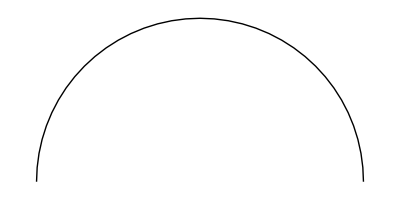

```mathematica
Graphics[Circle[{0,0},0.1,{0,1.π}]]
```

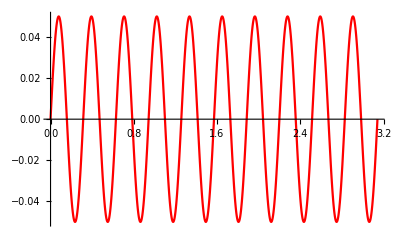

```mathematica
Plot[Sin[20x]/20,{x,0,π},PlotStyle->Red]
```

```mathematica
θ3=k/m2(1+2 m2/m1);
θ=θ3;
A={{2k- m1 θ,-k,-k},{-k,k-m2 θ,0},{-k,0,k-m2 θ}};
xv={x1,x2,x3};
Solve[A.xv==0,xv]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→-(m1 x1)/(2 m2),x3→-(m1 x1)/(2 m2)}}

```mathematica
T={{-L3 Sin[θ1]Cos[θ2+θ3]-L2 Sin[θ1]Cos[θ2]-L1 Sin[θ1],
-L3 Cos[θ1]Sin[θ2+θ3]-L2 Cos[θ1]Sin[θ2],
-L3 Cos[θ1] Sin[θ2+θ3]},
{L3 Cos[θ1]Cos[θ2+θ3]+L2 Cos[θ1]Cos[θ2]+L1 Cos[θ1],
  -L3 Sin[θ1]Sin[θ2+θ3]-L2 Sin[θ1]Sin[θ2],
  -L3 Sin[θ1]Sin[θ2+θ3]},
{0,L3 Cos[θ2+θ3]+L2 Cos[θ2],L3 Cos[θ2+θ3]}};
Det[T]//FullSimplify
%//TraditionalForm
```

-L2 L3 (L1+L2 Cos[θ2]+L3 Cos[θ2+θ3]) Sin[θ3]

-L2 L3 sin(θ3) (L1+L2 cos(θ2)+L3 cos(θ2+θ3))